```mathematica
(*Import packages*)
$LoadFeynArts = True;
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path,FileNameJoin[{NotebookDirectory[],"include"}]];
<< XSec`
<< TreeLevel`
<< CalcTools`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

CT::shdw: Symbol CT appears in multiple contexts {CalcTools`,Global`}; definitions in context CalcTools` may shadow or be shadowed by other definitions.

## Square amplitudes

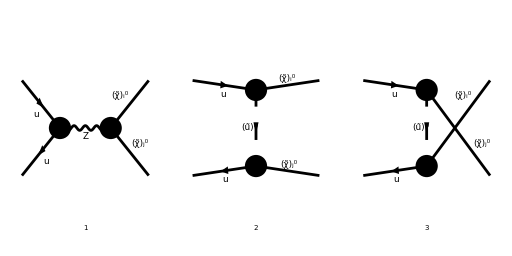

```mathematica
treeDiagrams = InsertFields[
CreateTopologies[0, 2->2,ExcludeTopologies->{Boxes,SelfEnergies,Tadpoles}], 
{F[3, {1,a}], -F[3, {1,b}]} -> {F[11, {i}], F[11, {j}]},
 InsertionLevel -> {Classes},
 Model -> MSSMQCD,
Restrictions->{NoLightFHCoupling,NoElectronHCoupling},
ExcludeParticles->{F[11],F[12],S[1],S[2],S[3],S[4]}
];
Paint[treeDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

```mathematica
Subscript[M, 0][0]=FCFAConvert[
CreateFeynAmp[treeDiagrams], 
IncomingMomenta->{ki,kj}, OutgoingMomenta->{pi,pj},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
SMP->True,
DropSumOver->True,
LorentzIndexNames->{μ,ν}
]/.AmpSimplifyRules/.{IndexDelta->FeynCalc`IndexDelta};
```

```mathematica
temp=SMP["g_W"]^2 FeynCalc`IndexDelta[a,b];
```

```mathematica
Subscript[M, 0][1]=temp*DiracSimplify/@(Convert2QZCharges/@(Subscript[M, 0][0]/temp));
Subscript[M, 0][2]=Subscript[M, 0][1]/.{Opp[i_,j_,L]*->-Opp[i,j,R]}//.SuperChargeRules;
```

```mathematica
MakeBoxes[DSf[s_,t_,g_],TraditionalForm]:=SubscriptBox["Δ",MakeBoxes[s,TraditionalForm]]
MakeBoxes[DSfC[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"*"]
MakeBoxes[DZ,TraditionalForm]=SubscriptBox["Δ","Z"];
MakeBoxes[FeynCalc`Index[Sfermion,a_],TraditionalForm]:=MakeBoxes[a,TraditionalForm]

MakeBoxes[Den[p2_,m2_],TraditionalForm]:=MakeBoxes[1/(p2-m2),TraditionalForm]
MakeBoxes[tMass[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"t"]
MakeBoxes[uMass[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"u"]
```

```mathematica
(*Subscript[M, s][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],1]]/.SMP["m_Z"]^2->DZ;
Subscript[M, t][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],2]]/.{SMP["m_Z"]^2->DZ,MSf[a_,t_,g_]^2->DSf[a,t,g]}/.Index[Sfermion,5]->Index[Sfermion,A];
Subscript[M, u][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],3]]/.{SMP["m_Z"]^2->DZ,MSf[a_,t_,g_]^2->DSf[a,t,g]}/.Index[Sfermion,5]->Index[Sfermion,A];*)
Subscript[M, s][0]=(Part[Subscript[M, 0][0],1]/.ZSimplifyRules//FeynAmpDenominatorExplicit)/.SMP["m_Z"]^2->DZ;
Subscript[M, t][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][0],2]//Convert2QZCharges]/.MSf[a_,t_,g_]^2->DSf[a,t,g]/.Index[Sfermion,5]->A;
Subscript[M, u][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][0],3]//Convert2QZCharges]/.MSf[a_,t_,g_]^2->DSf[a,t,g]/.Index[Sfermion,5]->A;
```

```mathematica
Subscript[M̄, s][0]=ConjugateAmplitude[Subscript[M, s][0]]/.{A->B,μ->ρ,ν->σ};
Subscript[M̄, t][0]=ConjugateAmplitude[Subscript[M, t][0]]/.{A->B,μ->ρ,ν->σ};
Subscript[M̄, u][0]=ConjugateAmplitude[Subscript[M, u][0]]/.{A->B,μ->ρ,ν->σ};
```

```mathematica
(*Square the amplitudes*)
Subscript[I, ss][0]=SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, s][0]];
Subscript[I, tt][0]=SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, t][0]];
Subscript[I, uu][0]=SquareAmplitudes[Subscript[M, u][0],Subscript[M̄, u][0]];
Subscript[I, st][0]=(SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, t][0]/.B->A]+SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, s][0]])/2;
Subscript[I, su][0]=(SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, u][0]/.B->A]+SquareAmplitudes[Subscript[M, u][0],Subscript[M̄, s][0]])/2;
Subscript[I, tu][0]=(SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, u][0]]+SquareAmplitudes[Subscript[M, u][0]/.A->B,Subscript[M̄, t][0]/.B->A])/2;
```

```mathematica
Subscript[I, ss][1]=FixDimension[Subscript[I, ss][0]/.Convert2Den];
Subscript[I, tt][1]=FixDimension[Subscript[I, tt][0]/.Convert2Den];
Subscript[I, uu][1]=FixDimension[Subscript[I, uu][0]/.Convert2Den];
Subscript[I, st][1]=FixDimension[Subscript[I, st][0]/.Convert2Den];
Subscript[I, su][1]=FixDimension[Subscript[I, su][0]/.Convert2Den];
Subscript[I, tu][1]=FixDimension[Subscript[I, tu][0]/.Convert2Den];
```

```mathematica
(*Common prefactor for the squared amplitudes.*)
Prefactor=4 (FeynCalc`IndexDelta[a,b])^2 SMP["g_W"]^4;
Subscript[I, ss][2]=Prefactor FactorDenominators[Subscript[I, ss][1]/Prefactor];
Subscript[I, tt][2]=Prefactor FactorDenominators[Subscript[I, tt][1]/Prefactor];
Subscript[I, uu][2]=Prefactor FactorDenominators[Subscript[I, uu][1]/Prefactor];
Subscript[I, st][2]=Prefactor FactorDenominators[Subscript[I, st][1]/Prefactor];
Subscript[I, su][2]=Prefactor FactorDenominators[Subscript[I, su][1]/Prefactor];
Subscript[I, tu][2]=Prefactor FactorDenominators[Subscript[I, tu][1]/Prefactor];
```

```mathematica
Prefactor Collect[
Expand[Subscript[I, ss][2]/Prefactor]/.{Opp[args__,L]*->-Opp[args,R],Opp[args__,R]*->-Opp[args,L]}//.SuperChargeRules,
{s*MNeu[i]*MNeu[j],(t-MNeu[i]^2)(t-MNeu[j]^2),(u-MNeu[i]^2)(u-MNeu[j]^2),t*u-MNeu[i]^2*MNeu[j]^2},
FullSimplify
]
```

4 g_W^4 δ_ab^2 (1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2) (-m_i^2 (-2 m_j^2+t+u)-m_j^2 (t+u)+t^2+u^2)-s m_i m_j 1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) ((Conjugate[(Z_s^L)])^2+(Conjugate[(Z_s^R)])^2+(Z_s^L)^2+(Z_s^R)^2))

```mathematica
(*Add squared amplitudes together, omitting prefactor and change to supercharges.*)
Itot[0]=(Subscript[I, ss][2]+Subscript[I, tt][2]+Subscript[I, uu][2]+2 Subscript[I, st][2]+2 Subscript[I, su][2]+2 Subscript[I, tu][2])/Prefactor;
Itot[1]=Collect[
Itot[0],
{s*MNeu[i]*MNeu[j],(t-MNeu[i]^2)(t-MNeu[j]^2),(u-MNeu[i]^2)(u-MNeu[j]^2),t*u-MNeu[i]^2*MNeu[j]^2},
(Collect[
#1,
Den[args1__]Den[args2__],
(FullSimplify[Expand[#1]/.{Opp[args__,L]*->-Opp[args,R],Opp[args__,R]*->-Opp[args,L]}//.SuperChargeRules]&)
]&)
]
```

(t-m_i^2) (t-m_j^2) (1/(t-Δ_A) 1/(t-Δ_B^*) (Q_B^(L R̄) Conjugate[(Q_A^(L R̄))]+Q_B^(R L̄) Conjugate[(Q_A^(R L̄))]+Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_B^(R R̄) Conjugate[(Q_A^(R R̄))])+1/(t-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Z_s^L Conjugate[(Q_A^(L L̄))]+Z_s^R Conjugate[(Q_A^(R R̄))])+1/(t-Δ_A^*) 1/(s-Δ_Z) (Q_A^(L L̄) Conjugate[(Z_s^L)]+Q_A^(R R̄) Conjugate[(Z_s^R)])+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))+(u-m_i^2) (u-m_j^2) (1/(u-Δ_A) 1/(u-Δ_B^*) (Q_A^(L R̄) Conjugate[(Q_B^(L R̄))]+Q_A^(R L̄) Conjugate[(Q_B^(R L̄))]+Q_A^(L L̄) Conjugate[(Q_B^(L L̄))]+Q_A^(R R̄) Conjugate[(Q_B^(R R̄))])+1/(u-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Q_A^(L L̄) Conjugate[(Z_s^L)]+Q_A^(R R̄) Conjugate[(Z_s^R)])+1/(u-Δ_A^*) 1/(s-Δ_Z) (Z_s^L Conjugate[(Q_A^(L L̄))]+Z_s^R Conjugate[(Q_A^(R R̄))])+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))+s m_i m_j (1/(t-Δ_A) 1/(u-Δ_B^*) (-Conjugate[(Q_A^(L L̄))] Conjugate[(Q_B^(L L̄))]-Conjugate[(Q_A^(R R̄))] Conjugate[(Q_B^(R R̄))])+1/(t-Δ_A^*) 1/(u-Δ_B) (-Q_A^(L L̄) Q_B^(L L̄)-Q_A^(R R̄) Q_B^(R R̄))+1/(t-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Conjugate[(Z_s^L)] (-Conjugate[(Q_A^(L L̄))])-Conjugate[(Z_s^R)] Conjugate[(Q_A^(R R̄))])+1/(u-Δ_A^*) 1/(s-Δ_Z) (Conjugate[(Z_s^L)] (-Conjugate[(Q_A^(L L̄))])-Conjugate[(Z_s^R)] Conjugate[(Q_A^(R R̄))])+1/(u-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Z_s^L (-Q_A^(L L̄))-Z_s^R Q_A^(R R̄))+1/(t-Δ_A^*) 1/(s-Δ_Z) (Z_s^L (-Q_A^(L L̄))-Z_s^R Q_A^(R R̄))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (-(Conjugate[(Z_s^L)])^2-(Conjugate[(Z_s^R)])^2-(Z_s^L)^2-(Z_s^R)^2))+(t u-m_i^2 m_j^2) (1/(t-Δ_A) 1/(u-Δ_B^*) (Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]+Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))])+1/(t-Δ_A^*) 1/(u-Δ_B) (Q_A^(R L̄) Q_B^(L R̄)+Q_A^(L R̄) Q_B^(R L̄)))

```mathematica
(*Show that the total amplitude can be written as effective charges in front of these four kinematic terms.*)
Collect[
Itot[1],
{s*MNeu[i]*MNeu[j],(t-MNeu[i]^2)(t-MNeu[j]^2),(u-MNeu[i]^2)(u-MNeu[j]^2),t*u-MNeu[i]^2*MNeu[j]^2},
(Isolate[#1//Simplify,IsolateNames->Q]&)
]
```

Q(1584) s m_i m_j+Q(1594) (t u-m_i^2 m_j^2)+Q(1589) (t-m_i^2) (t-m_j^2)+Q(1591) (u-m_i^2) (u-m_j^2)

```mathematica
DifferentialCrossSection=Prefactor/(64 Subscript[N, C]^2 π s^2)Itot[1]/.{(FeynCalc`IndexDelta[a,b])^p_->Subscript[N, C],SMP["g_W"]->Sqrt[4π Subscript[α, W]]}
```

1/(s^2 N_C)π α_W^2 ((t-m_i^2) (t-m_j^2) (1/(t-Δ_A) 1/(t-Δ_B^*) (Q_B^(L R̄) Conjugate[(Q_A^(L R̄))]+Q_B^(R L̄) Conjugate[(Q_A^(R L̄))]+Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_B^(R R̄) Conjugate[(Q_A^(R R̄))])+1/(t-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Z_s^L Conjugate[(Q_A^(L L̄))]+Z_s^R Conjugate[(Q_A^(R R̄))])+1/(t-Δ_A^*) 1/(s-Δ_Z) (Q_A^(L L̄) Conjugate[(Z_s^L)]+Q_A^(R R̄) Conjugate[(Z_s^R)])+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))+(u-m_i^2) (u-m_j^2) (1/(u-Δ_A) 1/(u-Δ_B^*) (Q_A^(L R̄) Conjugate[(Q_B^(L R̄))]+Q_A^(R L̄) Conjugate[(Q_B^(R L̄))]+Q_A^(L L̄) Conjugate[(Q_B^(L L̄))]+Q_A^(R R̄) Conjugate[(Q_B^(R R̄))])+1/(u-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Q_A^(L L̄) Conjugate[(Z_s^L)]+Q_A^(R R̄) Conjugate[(Z_s^R)])+1/(u-Δ_A^*) 1/(s-Δ_Z) (Z_s^L Conjugate[(Q_A^(L L̄))]+Z_s^R Conjugate[(Q_A^(R R̄))])+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))+s m_i m_j (1/(t-Δ_A) 1/(u-Δ_B^*) (-Conjugate[(Q_A^(L L̄))] Conjugate[(Q_B^(L L̄))]-Conjugate[(Q_A^(R R̄))] Conjugate[(Q_B^(R R̄))])+1/(t-Δ_A^*) 1/(u-Δ_B) (-Q_A^(L L̄) Q_B^(L L̄)-Q_A^(R R̄) Q_B^(R R̄))+1/(t-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Conjugate[(Z_s^L)] (-Conjugate[(Q_A^(L L̄))])-Conjugate[(Z_s^R)] Conjugate[(Q_A^(R R̄))])+1/(u-Δ_A^*) 1/(s-Δ_Z) (Conjugate[(Z_s^L)] (-Conjugate[(Q_A^(L L̄))])-Conjugate[(Z_s^R)] Conjugate[(Q_A^(R R̄))])+1/(u-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Z_s^L (-Q_A^(L L̄))-Z_s^R Q_A^(R R̄))+1/(t-Δ_A^*) 1/(s-Δ_Z) (Z_s^L (-Q_A^(L L̄))-Z_s^R Q_A^(R R̄))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (-(Conjugate[(Z_s^L)])^2-(Conjugate[(Z_s^R)])^2-(Z_s^L)^2-(Z_s^R)^2))+(t u-m_i^2 m_j^2) (1/(t-Δ_A) 1/(u-Δ_B^*) (Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]+Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))])+1/(t-Δ_A^*) 1/(u-Δ_B) (Q_A^(R L̄) Q_B^(L R̄)+Q_A^(L R̄) Q_B^(R L̄))))

## Integrate over t

```mathematica
(*To simplify before integrating over t, we will need to convert all terms containing u to t.*)
Itot[2]=Collect[
Itot[1]/.{Den[u,DSf[args__]]->-Den[t,uMass[args]],Den[u,DSfC[args__]]->-Den[t,uMass[args]*],Den[t,DSf[args__]]->Den[t,tMass[args]],Den[t,DSfC[args__]]->Den[t,tMass[args]*]}/.{u->MNeu[i]^2+MNeu[j]^2-s-t}//Expand,
Den[args1__]Den[args2__],
Simplify
]
```

1/(t-Conjugate[(Δ_B^u)]) 1/(t-Δ_A^t) (s (Conjugate[(Q_A^(L L̄))] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_A^(R R̄))] Conjugate[(Q_B^(R R̄))]) m_i m_j+Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))] ((m_j^2-t) m_i^2+t (-m_j^2+s+t))+Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))] ((m_j^2-t) m_i^2+t (-m_j^2+s+t)))+1/(t-Conjugate[(Δ_B^u)]) 1/(t-Δ_A^u) (-m_i^2+s+t) (-m_j^2+s+t) (Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)+Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)+Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)+Conjugate[(Q_B^(R R̄))] Q_A^(R R̄))+1/(t-Conjugate[(Δ_B^t)]) 1/(t-Δ_A^t) (t-m_i^2) (t-m_j^2) (Conjugate[(Q_A^(L L̄))] Q_B^(L L̄)+Conjugate[(Q_A^(L R̄))] Q_B^(L R̄)+Conjugate[(Q_A^(R L̄))] Q_B^(R L̄)+Conjugate[(Q_A^(R R̄))] Q_B^(R R̄))+1/(t-Conjugate[(Δ_A^t)]) 1/(t-Δ_B^u) (-((t-m_j^2) (Q_A^(R L̄) Q_B^(L R̄)+Q_A^(L R̄) Q_B^(R L̄)) m_i^2)+s m_j (Q_A^(L L̄) Q_B^(L L̄)+Q_A^(R R̄) Q_B^(R R̄)) m_i+t (-m_j^2+s+t) (Q_A^(R L̄) Q_B^(L R̄)+Q_A^(L R̄) Q_B^(R L̄)))+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_A^t) (-Conjugate[(Q_A^(L L̄))] (s Conjugate[(Z_s^L)] m_i m_j-(t-m_i^2) (t-m_j^2) Z_s^L)-Conjugate[(Q_A^(R R̄))] (s Conjugate[(Z_s^R)] m_i m_j-(t-m_i^2) (t-m_j^2) Z_s^R))+1/(s-Δ_Z) 1/(t-Conjugate[(Δ_A^u)]) (Conjugate[(Q_A^(L L̄))] (s Conjugate[(Z_s^L)] m_i m_j-(-m_i^2+s+t) (-m_j^2+s+t) Z_s^L)+Conjugate[(Q_A^(R R̄))] (s Conjugate[(Z_s^R)] m_i m_j-(-m_i^2+s+t) (-m_j^2+s+t) Z_s^R))+1/(s-Δ_Z) 1/(t-Conjugate[(Δ_A^t)]) (Conjugate[(Z_s^L)] (t-m_i^2) (t-m_j^2) Q_A^(L L̄)+Conjugate[(Z_s^R)] (t-m_i^2) (t-m_j^2) Q_A^(R R̄)-s m_i m_j (Q_A^(L L̄) Z_s^L+Q_A^(R R̄) Z_s^R))+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_A^u) (-Conjugate[(Z_s^L)] (-m_i^2+s+t) (-m_j^2+s+t) Q_A^(L L̄)-Conjugate[(Z_s^R)] (-m_i^2+s+t) (-m_j^2+s+t) Q_A^(R R̄)+s m_i m_j (Q_A^(L L̄) Z_s^L+Q_A^(R R̄) Z_s^R))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) ((s^2+2 t s+2 t^2-(s+2 t) m_j^2-m_i^2 (-2 m_j^2+s+2 t)) Abs[Z_s^L]^2+Abs[Z_s^R]^2 (s^2+2 t s+2 t^2-(s+2 t) m_j^2-m_i^2 (-2 m_j^2+s+2 t))-s m_i m_j ((Conjugate[(Z_s^L)])^2+(Conjugate[(Z_s^R)])^2+(Z_s^L)^2+(Z_s^R)^2))

```mathematica
(*Convert all t-dependence to a dictionary of standard t-integrals Subscript[T, d]^p(Subscript[Δ, 1],...,Subscript[Δ, d]).*)
ItotIntegrals[0]=ToTIntegrals[Itot[2]]
ItotIntegrals[1]=ReduceTIntegrals[ItotIntegrals[0]]
```

CT(1630) T_2^0(Conjugate[(Δ_B^t)],Conjugate[(Δ_A^t)])-CT(1637) T_2^1(Conjugate[(Δ_B^t)],Conjugate[(Δ_A^t)])+CT(1629) T_2^2(Conjugate[(Δ_B^t)],Conjugate[(Δ_A^t)])+CT(1628) T_2^0(Conjugate[(Δ_A^t)],Conjugate[(Δ_B^u)])+CT(1633) T_2^0(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^t)])+CT(1636) T_2^1(Conjugate[(Δ_A^t)],Conjugate[(Δ_B^u)])+CT(1638) T_2^1(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^t)])+CT(1626) T_2^2(Conjugate[(Δ_A^t)],Conjugate[(Δ_B^u)])+CT(1631) T_2^2(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^t)])+CT(1635) T_2^0(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^u)])+CT(1639) T_2^1(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^u)])+CT(1634) T_2^2(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^u)])+CT(1607) T_1^0(Conjugate[(Δ_A^t)])-CT(1621) T_1^1(Conjugate[(Δ_A^t)])+CT(1624) T_1^2(Conjugate[(Δ_A^t)])+CT(1612) T_1^0(Conjugate[(Δ_A^u)])-CT(1641) T_1^1(Conjugate[(Δ_A^u)])-CT(1643) T_1^2(Conjugate[(Δ_A^u)])+CT(1616) T_1^0(Δ_A^t)-CT(1642) T_1^1(Δ_A^t)+CT(1644) T_1^2(Δ_A^t)+CT(1618) T_1^0(Δ_A^u)-CT(1623) T_1^1(Δ_A^u)-CT(1625) T_1^2(Δ_A^u)+CT(1600) T_0^0+2 CT(1603) T_0^1+2 CT(1604) T_0^2

CT(1652) T_1^0(Conjugate[(Δ_A^t)])+CT(1657) T_1^0(Conjugate[(Δ_A^u)])+CT(1670) T_1^0(Δ_A^t)+CT(1664) T_1^0(Δ_A^u)+CT(1655) T_1^0(Conjugate[(Δ_B^t)])+CT(1660) T_1^0(Conjugate[(Δ_B^u)])+CT(1645) T_0^0+CT(1648) T_0^1+2 CT(1604) T_0^2

```mathematica
(*We can write it out in terms of the basic charges using GetKinematicCoefficients.*)
Collect[ItotIntegrals[0],tIntegral[args__],GetKinematicCoefficients]
```

m_i^2 (Conjugate[(Q_A^(L L̄))] Q_B^(L L̄)+Conjugate[(Q_A^(L R̄))] Q_B^(L R̄)+Conjugate[(Q_A^(R L̄))] Q_B^(R L̄)+Conjugate[(Q_A^(R R̄))] Q_B^(R R̄)) T_2^0(Conjugate[(Δ_B^t)],Conjugate[(Δ_A^t)]) m_j^2+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) ((-2 Abs[Z_s^L]^2-2 Abs[Z_s^R]^2) m_i^2+(-2 Abs[Z_s^L]^2-2 Abs[Z_s^R]^2) m_j^2+s (2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2)) T_0^1+(2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2) 1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) T_0^2+1/(s-Δ_Z) ((-Conjugate[(Z_s^L)] Q_A^(L L̄)-Conjugate[(Z_s^R)] Q_A^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Z_s^L)] Q_A^(L L̄)-Conjugate[(Z_s^R)] Q_A^(R R̄))) T_1^1(Conjugate[(Δ_A^t)])+1/(s-Conjugate[(Δ_Z)]) ((Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) m_i^2+s (-2 Conjugate[(Z_s^L)] Q_A^(L L̄)-2 Conjugate[(Z_s^R)] Q_A^(R R̄))+m_j^2 (Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄))) T_1^1(Δ_A^u)+1/(s-Δ_Z) (Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) T_1^2(Conjugate[(Δ_A^t)])+1/(s-Conjugate[(Δ_Z)]) (-Conjugate[(Z_s^L)] Q_A^(L L̄)-Conjugate[(Z_s^R)] Q_A^(R R̄)) T_1^2(Δ_A^u)+(m_i^2 (Q_A^(R L̄) Q_B^(L R̄)+Q_A^(L R̄) Q_B^(R L̄)) m_j^2+s m_i (Q_A^(L L̄) Q_B^(L L̄)+Q_A^(R R̄) Q_B^(R R̄)) m_j) T_2^0(Conjugate[(Δ_A^t)],Conjugate[(Δ_B^u)])+((Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]+Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))]) m_i^2 m_j^2+s (Conjugate[(Q_A^(L L̄))] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_A^(R R̄))] Conjugate[(Q_B^(R R̄))]) m_i m_j) T_2^0(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^t)])+((Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)+Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)+Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)+Conjugate[(Q_B^(R R̄))] Q_A^(R R̄)) s^2+m_i^2 (-Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)-Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)-Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)-Conjugate[(Q_B^(R R̄))] Q_A^(R R̄)) s+m_j^2 (-Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)-Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)-Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)-Conjugate[(Q_B^(R R̄))] Q_A^(R R̄)) s+m_i^2 m_j^2 (Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)+Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)+Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)+Conjugate[(Q_B^(R R̄))] Q_A^(R R̄))) T_2^0(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^u)])+((-Q_A^(R L̄) Q_B^(L R̄)-Q_A^(L R̄) Q_B^(R L̄)) m_i^2+m_j^2 (-Q_A^(R L̄) Q_B^(L R̄)-Q_A^(L R̄) Q_B^(R L̄))+s (Q_A^(R L̄) Q_B^(L R̄)+Q_A^(L R̄) Q_B^(R L̄))) T_2^1(Conjugate[(Δ_A^t)],Conjugate[(Δ_B^u)])+((-Conjugate[(Q_A^(L L̄))] Q_B^(L L̄)-Conjugate[(Q_A^(L R̄))] Q_B^(L R̄)-Conjugate[(Q_A^(R L̄))] Q_B^(R L̄)-Conjugate[(Q_A^(R R̄))] Q_B^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Q_A^(L L̄))] Q_B^(L L̄)-Conjugate[(Q_A^(L R̄))] Q_B^(L R̄)-Conjugate[(Q_A^(R L̄))] Q_B^(R L̄)-Conjugate[(Q_A^(R R̄))] Q_B^(R R̄))) T_2^1(Conjugate[(Δ_B^t)],Conjugate[(Δ_A^t)])+((-Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]-Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))]) m_i^2+(-Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]-Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))]) m_j^2+s (Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]+Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))])) T_2^1(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^t)])+((-Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)-Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)-Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)-Conjugate[(Q_B^(R R̄))] Q_A^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)-Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)-Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)-Conjugate[(Q_B^(R R̄))] Q_A^(R R̄))+s (2 Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)+2 Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)+2 Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)+2 Conjugate[(Q_B^(R R̄))] Q_A^(R R̄))) T_2^1(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^u)])+(Q_A^(R L̄) Q_B^(L R̄)+Q_A^(L R̄) Q_B^(R L̄)) T_2^2(Conjugate[(Δ_A^t)],Conjugate[(Δ_B^u)])+(Conjugate[(Q_A^(L L̄))] Q_B^(L L̄)+Conjugate[(Q_A^(L R̄))] Q_B^(L R̄)+Conjugate[(Q_A^(R L̄))] Q_B^(R L̄)+Conjugate[(Q_A^(R R̄))] Q_B^(R R̄)) T_2^2(Conjugate[(Δ_B^t)],Conjugate[(Δ_A^t)])+(Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]+Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))]) T_2^2(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^t)])+(Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)+Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)+Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)+Conjugate[(Q_B^(R R̄))] Q_A^(R R̄)) T_2^2(Conjugate[(Δ_B^u)],Conjugate[(Δ_A^u)])+1/(s-Δ_Z) T_1^2(Conjugate[(Δ_A^u)]) (-Conjugate[(Q_A^(L L̄))] Z_s^L-Conjugate[(Q_A^(R R̄))] Z_s^R)+1/(s-Conjugate[(Δ_Z)]) T_1^2(Δ_A^t) (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R)+1/(s-Conjugate[(Δ_Z)]) T_1^1(Δ_A^t) ((-Conjugate[(Q_A^(L L̄))] Z_s^L-Conjugate[(Q_A^(R R̄))] Z_s^R) m_i^2+m_j^2 (-Conjugate[(Q_A^(L L̄))] Z_s^L-Conjugate[(Q_A^(R R̄))] Z_s^R))+1/(s-Δ_Z) T_1^1(Conjugate[(Δ_A^u)]) ((Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R) m_i^2+s (-2 Conjugate[(Q_A^(L L̄))] Z_s^L-2 Conjugate[(Q_A^(R R̄))] Z_s^R)+m_j^2 (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R))+1/(s-Δ_Z) T_1^0(Conjugate[(Δ_A^u)]) ((-Conjugate[(Q_A^(L L̄))] Z_s^L-Conjugate[(Q_A^(R R̄))] Z_s^R) s^2+(Conjugate[(Q_A^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Q_A^(R R̄))] Conjugate[(Z_s^R)]) m_i m_j s+m_i^2 (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R) s+m_j^2 (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R) s+m_i^2 m_j^2 (-Conjugate[(Q_A^(L L̄))] Z_s^L-Conjugate[(Q_A^(R R̄))] Z_s^R))+1/(s-Conjugate[(Δ_Z)]) T_1^0(Δ_A^t) (m_i^2 (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R) m_j^2+s (-Conjugate[(Q_A^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Q_A^(R R̄))] Conjugate[(Z_s^R)]) m_i m_j)+1/(s-Δ_Z) T_1^0(Conjugate[(Δ_A^t)]) (m_i^2 (Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) m_j^2+s m_i (-Q_A^(L L̄) Z_s^L-Q_A^(R R̄) Z_s^R) m_j)+1/(s-Conjugate[(Δ_Z)]) T_1^0(Δ_A^u) ((-Conjugate[(Z_s^L)] Q_A^(L L̄)-Conjugate[(Z_s^R)] Q_A^(R R̄)) s^2+m_i^2 (Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) s+m_j^2 (Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) s+m_i m_j (Q_A^(L L̄) Z_s^L+Q_A^(R R̄) Z_s^R) s+m_i^2 m_j^2 (-Conjugate[(Z_s^L)] Q_A^(L L̄)-Conjugate[(Z_s^R)] Q_A^(R R̄)))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) T_0^0 ((Abs[Z_s^L]^2+Abs[Z_s^R]^2) s^2+(-Abs[Z_s^L]^2-Abs[Z_s^R]^2) m_i^2 s+(-Abs[Z_s^L]^2-Abs[Z_s^R]^2) m_j^2 s+m_i m_j (-(Conjugate[(Z_s^L)])^2-(Conjugate[(Z_s^R)])^2-(Z_s^L)^2-(Z_s^R)^2) s+(2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2) m_i^2 m_j^2)

```mathematica
(*A function for collecting all effective charges in an expression.*)
EffectiveCharges={
Qtu[args1__]Qtu[args2__],
Qtu[args1__]Qtu[args2__]*,
Qtu[args1__]*Qtu[args2__]*,
QtuC[args1__]QtuC[args2__],
QtuC[args1__]QtuC[args2__]*,
QtuC[args1__]*QtuC[args2__]*,
Zs[arg_]QtuC[args__],
Zs[arg_]*QtuC[args__],
Zs[arg_]QtuC[args__]*,
Zs[arg_]*QtuC[args__]*
};
CollectEffCharges[expr_]:=Collect2[
Collect[
FRH[expr]//Expand,
EffectiveCharges,
(Isolate[Simplify[#1//Expand]]&)
],
KK[arg_]
]
```

```mathematica
(*Write out the analytic results of all the Subscript[T, d]^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.*)
ItotIntegrals[2]=Collect[
Collect2[
FreeTIntegrals[ItotIntegrals[0]],
t1,
Simplify
]/.{t1^3->Subscript[Δ, t]''+t0^3,t1^2->Subscript[Δ, t]'+t0^2,t1^1->Subscript[Δ, t]+t0},
{Subscript[Δ, t],Subscript[Δ, t]',Subscript[Δ, t]'',Log[arg_]},
(Isolate[#1//CollectEffCharges]&)
]/.{Subscript[Δ, t]->t1-t0,Subscript[Δ, t]'->t1^2-t0^2,Subscript[Δ, t]''->t1^3-t0^3}
```

KK(1744) log((t1-Conjugate[(Δ_A^t)])/(t0-Conjugate[(Δ_A^t)]))+KK(1698) log((t1-Conjugate[(Δ_A^u)])/(t0-Conjugate[(Δ_A^u)]))+KK(1719) log((t1-Δ_A^t)/(t0-Δ_A^t))+KK(1734) log((t1-Δ_A^u)/(t0-Δ_A^u))+KK(1704) log((t1-Conjugate[(Δ_B^t)])/(t0-Conjugate[(Δ_B^t)]))+KK(1728) log((t1-Conjugate[(Δ_B^u)])/(t0-Conjugate[(Δ_B^u)]))+KK(1749) log((t1-Δ_B^u)/(t0-Δ_B^u))+2/3 KK(1692) (t1^3-t0^3)+KK(1691) (t1^2-t0^2)+KK(1685) (t1-t0)

```mathematica
(*Collect terms that can combine under A<->B.*)
(*BindexLogs={
Log[(t1-tMass[Index[Sfermion,B],args__]*)/(t0-tMass[Index[Sfermion,B],args__]*)],
Log[(t1-uMass[Index[Sfermion,B],args__]*)/(t0-uMass[Index[Sfermion,B],args__]*)],
Log[(t1-uMass[Index[Sfermion,B],args__])/(t0-uMass[Index[Sfermion,B],args__])]
};*)
BindexLogs={
Log[(t1-tMass[B,args__]*)/(t0-tMass[B,args__]*)],
Log[(t1-uMass[B,args__]*)/(t0-uMass[B,args__]*)],
Log[(t1-uMass[B,args__])/(t0-uMass[B,args__])]
};
ItotIntegrals[3]=Collect[
((((SelectNotFree[ItotIntegrals[2],BindexLogs])//FRH)/.A->C)/.{B->A,C->B})+SelectFree[ItotIntegrals[2],BindexLogs],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(1752) log((t1-Conjugate[(Δ_A^t)])/(t0-Conjugate[(Δ_A^t)]))+KK(1759) log((t1-Conjugate[(Δ_A^u)])/(t0-Conjugate[(Δ_A^u)]))+KK(1719) log((t1-Δ_A^t)/(t0-Δ_A^t))+KK(1765) log((t1-Δ_A^u)/(t0-Δ_A^u))+2/3 KK(1692) (t1^3-t0^3)+KK(1691) (t1^2-t0^2)+KK(1685) (t1-t0)

```mathematica
(*Conjugate total expression to assert if result is real.*)
ItotIntegralsC[0]=Refine[
Collect[
ItotIntegrals[3],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Conjugate[FRH[#1]]//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a*b*}&)
]/.{Log[arg_]->Log[arg*]}/.{Den[p_,m_]*->Den[p*,m*]},
Assumptions->{t1∈Reals,t0∈Reals,MNeu[i_]∈PositiveReals,s∈PositiveReals}
];
ItotIntegralsC[1]=Collect[
ItotIntegralsC[0],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(1752) log((t1-Conjugate[(Δ_A^t)])/(t0-Conjugate[(Δ_A^t)]))+KK(1759) log((t1-Conjugate[(Δ_A^u)])/(t0-Conjugate[(Δ_A^u)]))+KK(1719) log((t1-Δ_A^t)/(t0-Δ_A^t))+KK(1768) log((t1-Δ_A^u)/(t0-Δ_A^u))+2/3 KK(1692) (t1^3-t0^3)+KK(1691) (t1^2-t0^2)+KK(1685) (t1-t0)

```mathematica
FCCompareResults[FRH[ItotIntegrals[3]],FRH[ItotIntegralsC[1]],Text->{"\tResult is analytically real:","CORRECT.","WRONG!"},Interrupt->{Hold[Quit[1]],Automatic}];
```

Result is analytically real: CORRECT.

```mathematica
(*If the full integrated squared amplitude is real, we can replace the complex log-terms with their coefficients with just their real parts.*)
ItotIntegrals[4]=ItotIntegrals[3]//.{a_*Log[(t1-tMass[args__])/(t0-tMass[args__])]+b_*Log[(t1-tMass[args__]*)/(t0-tMass[args__]*)]->2Re[a*Log[(t1-tMass[args])/(t0-tMass[args])]],a_*Log[(t1-uMass[args__])/(t0-uMass[args__])]+b_*Log[(t1-uMass[args__]*)/(t0-uMass[args__]*)]->2Re[a*Log[(t1-uMass[args])/(t0-uMass[args])]]}
```

2 Re(KK(1719) log((t1-Δ_A^t)/(t0-Δ_A^t)))+2 Re(KK(1765) log((t1-Δ_A^u)/(t0-Δ_A^u)))+2/3 KK(1692) (t1^3-t0^3)+KK(1691) (t1^2-t0^2)+KK(1685) (t1-t0)

```mathematica
(*Substitute the tMass and uMass functions for their actual dependence on masses and decay rates (and s).*)
DeltaSubs={tMass[a_,args__]->MSf[a,args]^2-ⅈ*Subscript[Γ, a] MSf[a,args],uMass[a_,args__]->MNeu[i]^2+MNeu[j]^2-s-MSf[a,args]^2+ⅈ*Subscript[Γ, a] MSf[a,args],DZ->SMP["m_Z"]^2-ⅈ*Subscript[Γ, Z] SMP["m_Z"]};
DeltaAssumptions={MNeu[i_]∈PositiveReals,MSf[args__]∈PositiveReals,SMP["m_Z"]∈PositiveReals,Subscript[Γ, a_]∈PositiveReals,s∈PositiveReals};
ItotIntegrals[5]=Collect[
FRH[ItotIntegrals[4]],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Simplify[#1/.DeltaSubs,Assumptions->DeltaAssumptions]&)
]/.{Den[s_,m_]->1/(s-m)};
```

```mathematica
MakeBoxes[IdenticalPartFactor[i_,j_],TraditionalForm]:=SuperscriptBox[RowBox[{"(",FractionBox["1","2"],")"}],MakeBoxes[KroneckerDelta[i,j],TraditionalForm]]
(*IdenticalPartFactor[i_,j_]:=If[i==j,1/2,1]*)
```

```mathematica
TotalCrossSection=Simplify[(Prefactor/(64π Subscript[N, C]^2 s^2)IdenticalPartFactor[i,j]/.{(FeynCalc`IndexDelta[a,b])^p_->Subscript[N, C],SMP["g_W"]->Sqrt[4π Subscript[α, W]]})*ItotIntegrals[5]]
```

1/(s^2 N_C)π (1/2)^(i,j) α_W^2 (-(2 (t0^3-t1^3) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))/(3 (m_Z^4+(Γ_Z^2-2 s) m_Z^2+s^2))+2 (Re(log((-m_((q̃)_A)^2+ⅈ Γ_A m_((q̃)_A)+t1)/(-m_((q̃)_A)^2+ⅈ Γ_A m_((q̃)_A)+t0)) ((s (Conjugate[(Q_A^(L L̄))] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_A^(R R̄))] Conjugate[(Q_B^(R R̄))]) m_i m_j)/(-m_i^2-m_j^2+m_((q̃)_A)^2+m_((q̃)_B)^2+s-ⅈ m_((q̃)_A) Γ_A+ⅈ m_((q̃)_B) Γ_B)-(s (Conjugate[(Q_A^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Q_A^(R R̄))] Conjugate[(Z_s^R)]) m_i m_j)/(s-m_Z (m_Z+ⅈ Γ_Z))+((m_i^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)) (m_j^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)) (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R))/(s-m_Z (m_Z+ⅈ Γ_Z))-((Conjugate[(Q_A^(L L̄))] Q_B^(L L̄)+Conjugate[(Q_A^(L R̄))] Q_B^(L R̄)+Conjugate[(Q_A^(R L̄))] Q_B^(R L̄)+Conjugate[(Q_A^(R R̄))] Q_B^(R R̄)) (m_i^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)) (m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)-m_j^2))/(m_((q̃)_A)^2-ⅈ Γ_A m_((q̃)_A)-m_((q̃)_B) (m_((q̃)_B)+ⅈ Γ_B))+((Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]+Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))]) ((m_j^2-m_((q̃)_A)^2+ⅈ m_((q̃)_A) Γ_A) m_i^2+m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A) (-m_j^2+m_((q̃)_A)^2+s-ⅈ m_((q̃)_A) Γ_A)))/(-m_i^2-m_j^2+m_((q̃)_A)^2+m_((q̃)_B)^2+s-ⅈ m_((q̃)_A) Γ_A+ⅈ m_((q̃)_B) Γ_B)))+Re(log((-m_i^2-m_j^2+m_((q̃)_A)^2+s+t1-ⅈ m_((q̃)_A) Γ_A)/(-m_i^2-m_j^2+m_((q̃)_A)^2+s+t0-ⅈ m_((q̃)_A) Γ_A)) (-(s m_i m_j (Q_A^(L L̄) Q_B^(L L̄)+Q_A^(R R̄) Q_B^(R R̄)))/(-m_i^2-m_j^2+m_((q̃)_A)^2+m_((q̃)_B)^2+s-ⅈ m_((q̃)_A) Γ_A+ⅈ m_((q̃)_B) Γ_B)+(s m_i m_j (Q_A^(L L̄) Z_s^L+Q_A^(R R̄) Z_s^R))/(s-m_Z (m_Z+ⅈ Γ_Z))+((Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)+Conjugate[(Q_B^(L R̄))] Q_A^(L R̄)+Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)+Conjugate[(Q_B^(R R̄))] Q_A^(R R̄)) (m_j^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)) (m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)-m_i^2))/(m_((q̃)_A)^2-ⅈ Γ_A m_((q̃)_A)-m_((q̃)_B) (m_((q̃)_B)+ⅈ Γ_B))-((Q_A^(R L̄) Q_B^(L R̄)+Q_A^(L R̄) Q_B^(R L̄)) ((m_j^2-m_((q̃)_A)^2+ⅈ m_((q̃)_A) Γ_A) m_i^2+m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A) (-m_j^2+m_((q̃)_A)^2+s-ⅈ m_((q̃)_A) Γ_A)))/(-m_i^2-m_j^2+m_((q̃)_A)^2+m_((q̃)_B)^2+s-ⅈ m_((q̃)_A) Γ_A+ⅈ m_((q̃)_B) Γ_B)+((Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) (m_j^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)) (m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)-m_i^2))/(s-m_Z (m_Z+ⅈ Γ_Z)))))-((t0^2-t1^2) ((-m_i^2-m_j^2+s) Abs[Z_s^L]^2+Abs[Z_s^R]^2 (-m_i^2-m_j^2+s)-ⅈ m_Z Γ_Z (Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)-Conjugate[(Q_A^(L L̄))] Z_s^L-Conjugate[(Q_A^(R R̄))] Z_s^R)))/(m_Z^4+(Γ_Z^2-2 s) m_Z^2+s^2)+(t1-t0) (Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]+Q_A^(L R̄) Conjugate[(Q_B^(L R̄))]+Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))]+Conjugate[(Q_B^(L L̄))] Q_A^(L L̄)+Conjugate[(Q_B^(R L̄))] Q_A^(R L̄)+Conjugate[(Q_B^(R R̄))] Q_A^(R R̄)+Conjugate[(Q_A^(L L̄))] Q_B^(L L̄)+Conjugate[(Q_A^(L R̄))] Q_B^(L R̄)+Q_A^(R L̄) Q_B^(L R̄)+Conjugate[(Q_A^(R L̄))] Q_B^(R L̄)+Q_A^(L R̄) Q_B^(R L̄)+Conjugate[(Q_A^(R R̄))] Q_B^(R R̄)+(Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) ((m_((q̃)_A)^2-ⅈ Γ_A m_((q̃)_A)-s)/(s-m_Z (m_Z+ⅈ Γ_Z))-(m_i^2+m_j^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A))/(-m_Z^2+ⅈ Γ_Z m_Z+s))+((m_((q̃)_A)^2+ⅈ Γ_A m_((q̃)_A)-s)/(-m_Z^2+ⅈ Γ_Z m_Z+s)-(m_i^2+m_j^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A))/(s-m_Z (m_Z+ⅈ Γ_Z))) (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R)+((s (s-m_j^2)-m_i^2 (s-2 m_j^2)) Abs[Z_s^L]^2+Abs[Z_s^R]^2 (s (s-m_j^2)-m_i^2 (s-2 m_j^2))-s m_i m_j ((Conjugate[(Z_s^L)])^2+(Conjugate[(Z_s^R)])^2+(Z_s^L)^2+(Z_s^R)^2))/(m_Z^4+(Γ_Z^2-2 s) m_Z^2+s^2)))

```mathematica
%//.{a_*b_+a_*b_*->2Re[a*b],a_*b_*+a_**b->2Re[a*b*],a_*a_*->Abs[a]^2}
```

```mathematica
ItotIntegrals[5]=Collect[
FRH[ItotIntegrals[4]]/.{B->A},
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Simplify[#1/.DeltaSubs,Assumptions->DeltaAssumptions]&)
]/.Den[s_,m_]->1/(s-m)
```

(2 (t1^3-t0^3) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))/(3 (s-m_Z (m_Z-ⅈ Γ_Z)) (s-m_Z (m_Z+ⅈ Γ_Z)))+2 (Re(log((-m_((q̃)_A)^2+ⅈ Γ_A m_((q̃)_A)+t1)/(-m_((q̃)_A)^2+ⅈ Γ_A m_((q̃)_A)+t0)) ((s ((Conjugate[(Q_A^(L L̄))])^2+(Conjugate[(Q_A^(R R̄))])^2) m_i m_j)/(-m_i^2-m_j^2+2 m_((q̃)_A)^2+s)-(s (Conjugate[(Q_A^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Q_A^(R R̄))] Conjugate[(Z_s^R)]) m_i m_j)/(s-m_Z (m_Z+ⅈ Γ_Z))+((Conjugate[(Q_A^(L L̄))] Q_A^(L L̄)+Conjugate[(Q_A^(L R̄))] Q_A^(L R̄)+Conjugate[(Q_A^(R L̄))] Q_A^(R L̄)+Conjugate[(Q_A^(R R̄))] Q_A^(R R̄)) (m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)-m_i^2) (m_((q̃)_A) (ⅈ m_((q̃)_A)+Γ_A)-ⅈ m_j^2))/(2 m_((q̃)_A) Γ_A)+(2 Conjugate[(Q_A^(L R̄))] Conjugate[(Q_A^(R L̄))] ((m_j^2-m_((q̃)_A)^2+ⅈ m_((q̃)_A) Γ_A) m_i^2+m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A) (-m_j^2+m_((q̃)_A)^2+s-ⅈ m_((q̃)_A) Γ_A)))/(-m_i^2-m_j^2+2 m_((q̃)_A)^2+s)+((m_i^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)) (m_j^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)) (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R))/(s-m_Z (m_Z+ⅈ Γ_Z))))+Re(log((-m_i^2-m_j^2+m_((q̃)_A)^2+s+t1-ⅈ m_((q̃)_A) Γ_A)/(-m_i^2-m_j^2+m_((q̃)_A)^2+s+t0-ⅈ m_((q̃)_A) Γ_A)) (-(s m_i m_j ((Q_A^(L L̄))^2+(Q_A^(R R̄))^2))/(-m_i^2-m_j^2+2 m_((q̃)_A)^2+s)+((Conjugate[(Q_A^(L L̄))] Q_A^(L L̄)+Conjugate[(Q_A^(L R̄))] Q_A^(L R̄)+Conjugate[(Q_A^(R L̄))] Q_A^(R L̄)+Conjugate[(Q_A^(R R̄))] Q_A^(R R̄)) (m_i^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)) (m_((q̃)_A) (ⅈ m_((q̃)_A)+Γ_A)-ⅈ m_j^2))/(2 m_((q̃)_A) Γ_A)-(2 Q_A^(L R̄) Q_A^(R L̄) ((m_j^2-m_((q̃)_A)^2+ⅈ m_((q̃)_A) Γ_A) m_i^2+m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A) (-m_j^2+m_((q̃)_A)^2+s-ⅈ m_((q̃)_A) Γ_A)))/(-m_i^2-m_j^2+2 m_((q̃)_A)^2+s)+(s m_i m_j (Q_A^(L L̄) Z_s^L+Q_A^(R R̄) Z_s^R))/(s-m_Z (m_Z+ⅈ Γ_Z))+((Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) (m_j^2-m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)) (m_((q̃)_A) (m_((q̃)_A)-ⅈ Γ_A)-m_i^2))/(s-m_Z (m_Z+ⅈ Γ_Z)))))+1/2 (t1^2-t0^2) ((2 (Abs[Z_s^L]^2+Abs[Z_s^R]^2) (-m_i^2-m_j^2+s))/((s-m_Z (m_Z-ⅈ Γ_Z)) (s-m_Z (m_Z+ⅈ Γ_Z)))+(Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) (1/(s-m_Z (m_Z-ⅈ Γ_Z))-1/(s-m_Z (m_Z+ⅈ Γ_Z)))+(1/(s-m_Z (m_Z+ⅈ Γ_Z))-1/(s-m_Z (m_Z-ⅈ Γ_Z))) (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R))+(t1-t0) (2 Conjugate[(Q_A^(L R̄))] Conjugate[(Q_A^(R L̄))]+2 Q_A^(R L̄) Conjugate[(Q_A^(R L̄))]+2 Conjugate[(Q_A^(L L̄))] Q_A^(L L̄)+2 Conjugate[(Q_A^(L R̄))] Q_A^(L R̄)+2 Q_A^(L R̄) Q_A^(R L̄)+2 Conjugate[(Q_A^(R R̄))] Q_A^(R R̄)+(Conjugate[(Z_s^L)] Q_A^(L L̄)+Conjugate[(Z_s^R)] Q_A^(R R̄)) ((m_((q̃)_A)^2-ⅈ Γ_A m_((q̃)_A)-s)/(s-m_Z (m_Z+ⅈ Γ_Z))-(m_i^2+m_j^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A))/(s-m_Z (m_Z-ⅈ Γ_Z)))+((m_((q̃)_A)^2+ⅈ Γ_A m_((q̃)_A)-s)/(s-m_Z (m_Z-ⅈ Γ_Z))-(m_i^2+m_j^2-m_((q̃)_A)^2+ⅈ m_((q̃)_A) Γ_A)/(s-m_Z (m_Z+ⅈ Γ_Z))) (Conjugate[(Q_A^(L L̄))] Z_s^L+Conjugate[(Q_A^(R R̄))] Z_s^R)+((s (s-m_j^2)-m_i^2 (s-2 m_j^2)) Abs[Z_s^L]^2+Abs[Z_s^R]^2 (s (s-m_j^2)-m_i^2 (s-2 m_j^2))-s m_i m_j ((Conjugate[(Z_s^L)])^2+(Conjugate[(Z_s^R)])^2+(Z_s^L)^2+(Z_s^R)^2))/((s-m_Z (m_Z-ⅈ Γ_Z)) (s-m_Z (m_Z+ⅈ Γ_Z))))

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"results"}]];
Directory[];
```

```mathematica
(*Subscript[I, ss][1]>>Iss.txt
Subscript[I, tt][1]>>Itt.txt
Subscript[I, uu][1]>>Iuu.txt
Subscript[I, st][1]>>Ist.txt
Subscript[I, su][1]>>Isu.txt
Subscript[I, tu][1]>>Itu.txt*)
```